## 获取卷积核

```mathematica
GetChesses[core_]:=Module[{nears,corner},
nears=(ListConvolve[({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),ArrayPad[core,1,0]](1-core))/.{n_/;n>0->1};
corner=(1-core)(1-nears)*(ListConvolve[({{1, 0, 1}, {0, 0, 0}, {1, 0, 1}}),ArrayPad[core,1,0]]);
{core,nears,corner}
]
```

```mathematica
MatrixForm/@GetChesses[({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
MatrixForm/@GetChesses[({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)}

## 变换操作

```mathematica
RightRotate[m_]:=Reverse/@Transpose[m]
RightRotate[m_,n_]:=Nest[Reverse/@Transpose[#]&,m,n]
```

```mathematica
LeftRotate[m_]:=RightRotate[m,3]
LeftRotate[m_,n_]:=RightRotate[m,4-n]
```

```mathematica
Keep[m_]:=m
Reflect[m_]:=Reverse[m]
```

```mathematica
RightRotate[({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}}),4]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

## 排除重复

### 穷举所有操作：

```mathematica
GetAllChesses[m_]:=Flatten[Table[f2@f1[f0[m],n],{f0,{Keep,Reflect}},{f1,{RightRotate}},{f2,{Keep,Reflect}},{n,1,4}],3]
```

```mathematica
Tally[MatrixForm/@GetAllChesses[({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})]]
```

{{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),2},{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),2},{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),2},{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),2},{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),2},{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),2},{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),2},{(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0),2}}

### 获取不重复棋子

```mathematica
TallyChesses[m_]:=Tally[GetAllChesses[m]]ᵀ⟦1⟧
```

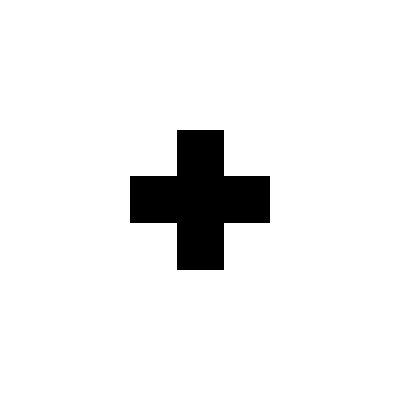

```mathematica
ArrayPlot/@TallyChesses[({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})]
```

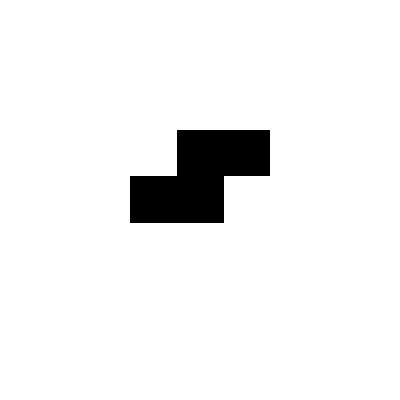
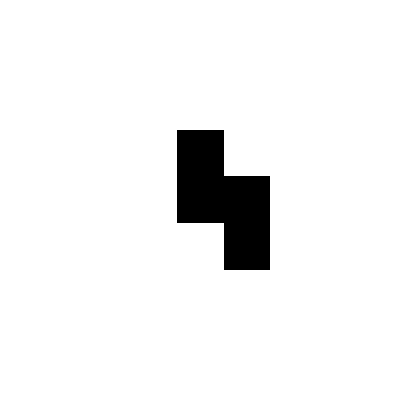
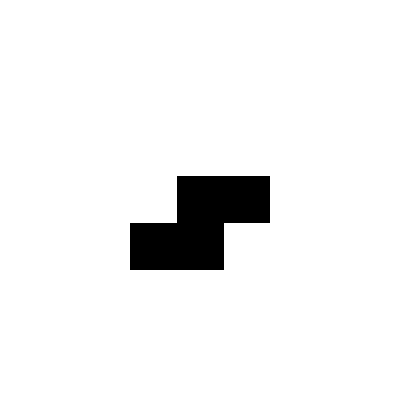
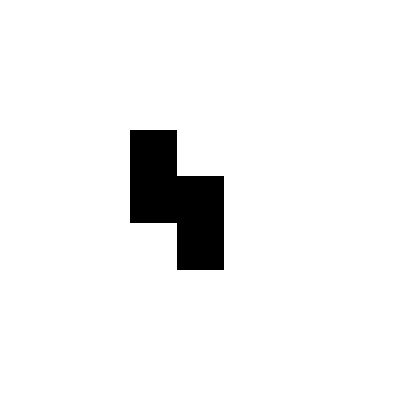
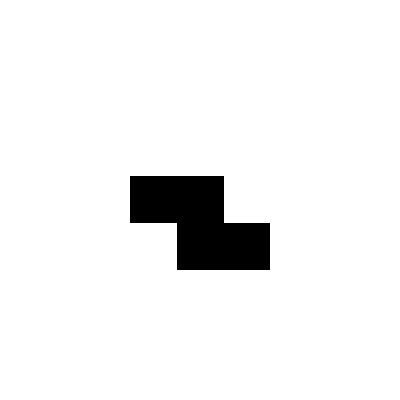
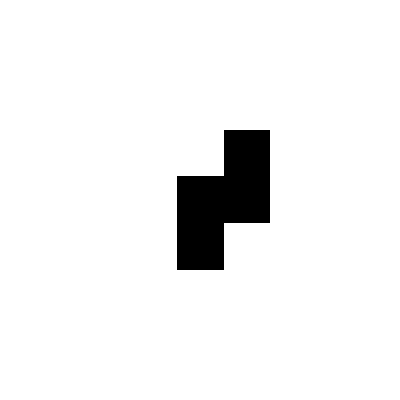
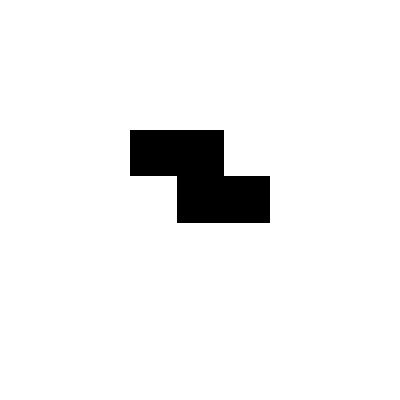
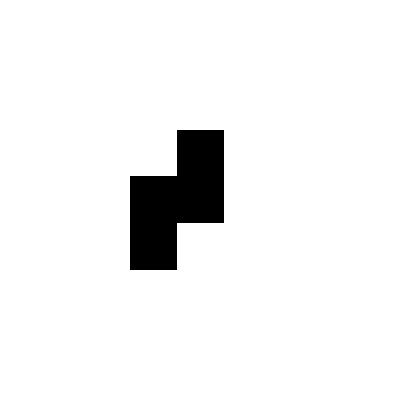

```mathematica
ArrayPlot/@TallyChesses[({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})]
```